```mathematica
X = PauliMatrix[1];
Z = PauliMatrix[3];
Id = PauliMatrix[0];
Had = 1/Sqrt[2] {{1,1},{1,-1}};
ket0 = {{1},{0}};
ket1 = {{0},{1}};
(*4 qubit VQLS*)
(*A = 1/ζ(∑_(j=1)^n Subscript[X, j]+J∑_(j=1)^(n-1) Subscript[Z, j] Subscript[Z, j+1]+ηI)
b=H^(⊗n)|0>
*)
κ = 20;
ASym [ζ_, η_] := 1/ζ (X1+X2+X3+X4+
J *(
Z1Z2+Z2Z3+
Z3Z4
))+η IdentityMatrix[2^4];
```

```mathematica
J = 0.1;
A[ζ_, η_] := 1/ζ (KroneckerProduct[X, KroneckerProduct[Id, KroneckerProduct[Id, Id]]]+KroneckerProduct[Id, KroneckerProduct[X, KroneckerProduct[Id, Id]]]+KroneckerProduct[Id, KroneckerProduct[Id, KroneckerProduct[X, Id]]]+KroneckerProduct[Id, KroneckerProduct[Id, KroneckerProduct[Id, X]]]+
J *(
KroneckerProduct[Z, KroneckerProduct[Z, KroneckerProduct[Id, Id]]]+KroneckerProduct[Id, KroneckerProduct[Z, KroneckerProduct[Z, Id]]]+
KroneckerProduct[Id, KroneckerProduct[Id, KroneckerProduct[Z, Z]]]
)+η IdentityMatrix[2^4]);
```

```mathematica
b = KroneckerProduct[Had, Had, Had, Had].KroneckerProduct[ket0, ket0, ket0, ket0]
```

{{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4}}

```mathematica
x = Inverse[A[5,1] ].b
```

{{0.182233},{0.227947},{0.278602},{0.215367},{0.278602},{0.338433},{0.263226},{0.227947},{0.227947},{0.263226},{0.338433},{0.278602},{0.215367},{0.278602},{0.227947},{0.182233}}

```mathematica
x/Norm[x]
```

{{0.178254},{0.222969},{0.272518},{0.210664},{0.272518},{0.331043},{0.257478},{0.222969},{0.222969},{0.257478},{0.331043},{0.272518},{0.210664},{0.272518},{0.222969},{0.178254}}

```mathematica
(x/Norm[x])^2
```

{{0.0317744},{0.0497152},{0.074266},{0.0443791},{0.074266},{0.109589},{0.0662948},{0.0497152},{0.0497152},{0.0662948},{0.109589},{0.074266},{0.0443791},{0.074266},{0.0497152},{0.0317744}}

```mathematica
A[5,1]
```

{{0.26,0.2,0.2,0.,0.2,0.,0.,0.,0.2,0.,0.,0.,0.,0.,0.,0.},{0.2,0.22,0.,0.2,0.,0.2,0.,0.,0.,0.2,0.,0.,0.,0.,0.,0.},{0.2,0.,0.18,0.2,0.,0.,0.2,0.,0.,0.,0.2,0.,0.,0.,0.,0.},{0.,0.2,0.2,0.22,0.,0.,0.,0.2,0.,0.,0.,0.2,0.,0.,0.,0.},{0.2,0.,0.,0.,0.18,0.2,0.2,0.,0.,0.,0.,0.,0.2,0.,0.,0.},{0.,0.2,0.,0.,0.2,0.14,0.,0.2,0.,0.,0.,0.,0.,0.2,0.,0.},{0.,0.,0.2,0.,0.2,0.,0.18,0.2,0.,0.,0.,0.,0.,0.,0.2,0.},{0.,0.,0.,0.2,0.,0.2,0.2,0.22,0.,0.,0.,0.,0.,0.,0.,0.2},{0.2,0.,0.,0.,0.,0.,0.,0.,0.22,0.2,0.2,0.,0.2,0.,0.,0.},{0.,0.2,0.,0.,0.,0.,0.,0.,0.2,0.18,0.,0.2,0.,0.2,0.,0.},{0.,0.,0.2,0.,0.,0.,0.,0.,0.2,0.,0.14,0.2,0.,0.,0.2,0.},{0.,0.,0.,0.2,0.,0.,0.,0.,0.,0.2,0.2,0.18,0.,0.,0.,0.2},{0.,0.,0.,0.,0.2,0.,0.,0.,0.2,0.,0.,0.,0.22,0.2,0.2,0.},{0.,0.,0.,0.,0.,0.2,0.,0.,0.,0.2,0.,0.,0.2,0.18,0.,0.2},{0.,0.,0.,0.,0.,0.,0.2,0.,0.,0.,0.2,0.,0.2,0.,0.22,0.2},{0.,0.,0.,0.,0.,0.,0.,0.2,0.,0.,0.,0.2,0.,0.2,0.2,0.26}}

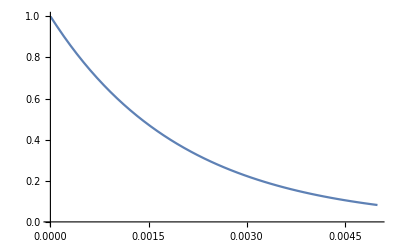

```mathematica
Plot[Exp[-500.  t], {t, 0.0000021, 0.005}]
```

```mathematica
Exp[-500 0.000021]
```

0.900325